## From Input to Graph to visualize Petri Net.

```mathematica
systemTransitions={ {<|"Combine"->rate|>,{{"H2",2},{"O2",1}}-> {{"H2O",2}}},
{<|"Hydrolysis"->rate2|>,{{"H2O",2}}-> {{"H2",2},{"O2",1}}}}
```

{{<|Combine→rate|>,{{H2,2},{O2,1}}→{{H2O,2}}},{<|Hydrolysis→rate2|>,{{H2O,2}}→{{H2,2},{O2,1}}}}

```mathematica
systemInitials =<|"H2"->a1,"O2"->b1,"H2O"->c1|>
```

<|H2→a1,O2→b1,H2O→c1|>

```mathematica
pCapacities = KeyMap[p,systemInitials]
```

<|p[H2]→a1,p[O2]→b1,p[H2O]→c1|>

```mathematica
tCapacities =KeyMap[t,Association[First/@systemTransitions]]
```

<|t[Combine]→rate,t[Hydrolysis]→rate2|>

```mathematica
initialValue[x_]:=Lookup[systemInitials,x,0]
```

```mathematica
initialValue["O2"]
```

b1

```mathematica
makeEdges[{transition_,sourcePlaces_->sinkPlaces_}]:= Module[{sourceEdges,sinkEdges} ,sourceEdges=DirectedEdge[p[First@#],t[First@Keys@transition]]->Last@#&/@sourcePlaces;sinkEdges=DirectedEdge[t[First@Keys@transition],p[First@#]]->Last@#&/@sinkPlaces;
Join[sourceEdges,sinkEdges]
]
```

```mathematica
edgeData= Join@@makeEdges/@systemTransitions
```

{p[H2]->t[Combine]→2,p[O2]->t[Combine]→1,t[Combine]->p[H2O]→2,p[H2O]->t[Hydrolysis]→2,t[Hydrolysis]->p[H2]→2,t[Hydrolysis]->p[O2]→1}

```mathematica
{edgeList,edgeWeights}={Keys@edgeData,Values@edgeData}
```

{{p[H2]->t[Combine],p[O2]->t[Combine],t[Combine]->p[H2O],p[H2O]->t[Hydrolysis],t[Hydrolysis]->p[H2],t[Hydrolysis]->p[O2]},{2,1,2,2,2,1}}

```mathematica
ClearAll[vsf];
vsf[scale_][pos_,p[v_],size_]:= {Circle[pos,scale First@size],Inset[v,pos]}
vsf[scale_][pos_,t[v_],size_]:= {{Transparent,Rectangle[pos- scale size,pos+scale size]},Inset[v,pos]}
```

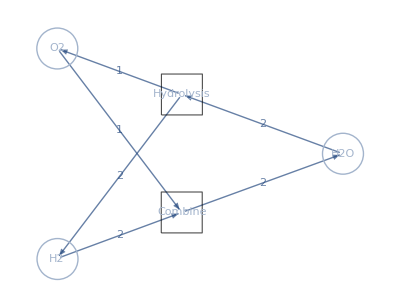

```mathematica
pNet = Graph[edgeList,VertexShapeFunction-> vsf[6],EdgeWeight->edgeWeights,EdgeLabels->"EdgeWeight"]
```

## Dynamic Analysis Using State values in Petri Net.

```mathematica
VertexList[pNet]
```

{p[H2],t[Combine],p[O2],p[H2O],t[Hydrolysis]}

```mathematica
EdgeList[pNet]
```

{p[H2]->t[Combine],p[O2]->t[Combine],t[Combine]->p[H2O],p[H2O]->t[Hydrolysis],t[Hydrolysis]->p[H2],t[Hydrolysis]->p[O2]}

define a pNetData function to return the data structure of Petri Net created.
returns a list of vertex and the data related to them:
{veretx1, vertex2, vertex3, vertex4,...}
vertex_i = {vertex label , Quantity[time],
{ States it can move to:{vertex1, edgeweight1},{vertex2,edgeweight2},...},
{ States it be from: {vertex3, edgeweight3},{vertex3,edgeweight3},...}
}
For example:
{ {“H2”,  a1[t], {“H2O”, rate, 2, 2}}, {“O2”, b1[t], {“H2O”, rate, 1, 2}},  {“H2O”, c1[t],  { {“H2”, rate2, 2, 2}, {“O2”, rate2, 2, 1} }